2.

Plot3D::nonopt: Options expected (instead of {y,-10,10}) beyond position 3 in Plot3D[F[x,y],{y y≤x&&x≤3},{x,-10,10},{y,-10,10}]. An option must be a rule or a list of rules.

Plot3D[F[x,y],{y y≤x&&x≤3},{x,-10,10},{y,-10,10}]

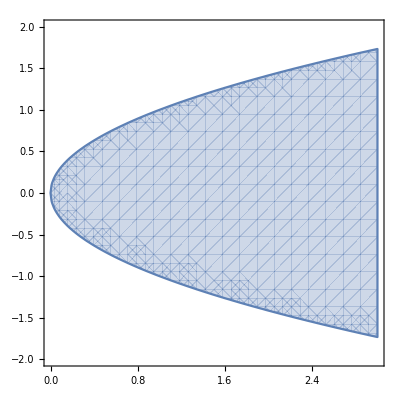

```mathematica
F[x_,y_]=2.

Plot3D[F[x,y],{y*y≤x&&x≤3},{x,-10,10},{y,-10,10}]

RegionPlot[y*y≤x&&x≤3,{x,0,3},{y,-2,2}]
```

```mathematica
Plot3D[F[x,y],{y y≤x&&x≤3},{x,0,3},{y,-2,2}]
```

Plot3D::nonopt: Options expected (instead of {y,-2,2}) beyond position 3 in Plot3D[F[x,y],{y y≤x&&x≤3},{x,0,3},{y,-2,2}]. An option must be a rule or a list of rules.

```mathematica
V[x_,y_]=∫_0^3 ∫_(-√x)^(√x) 2ⅆyⅆx
```

8 √3

```mathematica
N[8 √3]
```

13.8564

```mathematica
S[y_]=2*∫_(-√3)^(√3) (3-y*y)ⅆy
```

8 √3

```mathematica
N[8 √3]
```

13.8564

Plot3D::nonopt: Options expected (instead of {y,-10,10}) beyond position 3 in Plot3D[F[x,y],{y y≤x&&x≤3},{x,-10,10},{y,-10,10}]. An option must be a rule or a list of rules.

-Graphics3D-

Integrate::diffend: ∫_x^3 1ⅆx∫_(y*y)^x 1ⅆy cannot be interpreted since ⅆx is followed by ∫_(y*y)^x 1ⅆy. It may be necessary to use parentheses to ensure that ⅆx appears at the end of the integral.